## 3 - different trials of post value vectors (“Rinse & repeat”)

```mathematica
SetDirectory["~/Documents/Processing/MIDIDance/RinseAndRepeat"];
nrSignals=6;
```

```mathematica
ImportProcessingHitOutput[filename_String,nrSignals_Integer]:=Module[{data,lengthSignals,xdatasep},
data=Import[filename,"CSV"];
lengthSignals=(Length[First@data]-3)/nrSignals;
xdatasep=({#⟦2;;3⟧,Partition[#⟦4;;-1⟧,lengthSignals]}&/@data);
Return[xdatasep]
];
```

```mathematica
filelist=FileNames["*.txt"];
signallist={};
Do[
AppendTo[signallist,ImportProcessingHitOutput[fname,nrSignals]];
Print["Loaded file '"<>fname<>"'."];
,{fname,filelist}]
```

Loaded file 'test1.txt'.

Loaded file 'test2.txt'.

Loaded file 'test3.txt'.

Loaded file 'test4.txt'.

Loaded file 'test5.txt'.

```mathematica
xplots={};
trange=1;;15;
trial=0;
Do[
meantraces=Last@Transpose@Cases[data,{{axis=2,_},__}];
actualplot=ListPlot[Mean[meantraces]⟦1;;3,trange⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{-0.2,1.2},PlotLabel->"actual hit on axis #"<>ToString@axis<>"\nhand #0, trial #"<>ToString[trial]];
meantraces=Last@Transpose@Cases[data,{{_,axis},__}];
shouldhavebeenplot=ListPlot[Mean[meantraces]⟦1;;3,trange⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{-0.2,1.2},PlotLabel->"should have been hit on axis #"<>ToString@axis<>"\nhand #0, trial #"<>ToString[trial++]];

AppendTo[xplots,{actualplot,shouldhavebeenplot}];
,{data,signallist}];
Clear[meantraces,actualplot,shouldhavebeenplot];
GraphicsGrid[xplots,ImageSize->700]
```

#### Recordings across trials

```mathematica
alldata=Flatten[signallist,1];
```

```mathematica
recordedSituatons=Union@alldata⟦All,1⟧
```

{{0,-1},{0,0},{0,2},{0,3},{1,-1},{1,0},{1,1},{1,2},{1,3},{2,0},{2,2},{3,-1},{3,3},{3,4},{3,5},{4,-1},{4,3},{4,4},{4,5},{5,-1},{5,3},{5,5}}

```mathematica
RecordingsWithAxis[datasep_List,axisActual_,axisTarget_]:=Last@Transpose@Cases[datasep,{{axisActual,axisTarget},__}];
RecordingsActualAxis[datasep_List,axis_Integer]:=RecordingsWithAxis[datasep,axis,_];
RecordingsTargetAxis[datasep_List,axis_Integer]:=RecordingsWithAxis[datasep,_,axis];
CorrectFraction[datasep_List,axis_Integer]:=Module[{nrTargettingThisAxis,nrTargettingAndHittingThisAxis,f=0},
nrTargettingThisAxis=Length@RecordingsTargetAxis[datasep,axis];
If[nrTargettingThisAxis>0,
nrTargettingAndHittingThisAxis=Length@RecordingsWithAxis[datasep,axis,axis];
f=nrTargettingAndHittingThisAxis/nrTargettingThisAxis;
];
Return[f];
];
```

```mathematica
rangeOfHand={1;;3,4;;6};
trange={0,14.5};
GraphicsGrid[
Table[ListPlot[Mean[xd=RecordingsActualAxis[alldata,axisID+3*handID]⟦All,rangeOfHand⟦handID+1⟧⟧],Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->"hand #"<>ToString[handID]<>": actual hit on axis #"<>ToString[axisID+3*handID]<>"\nN = "<>ToString[Length@xd],ImageSize->200],{handID,0,1},{axisID,0,2}],
ImageSize->1000
]

GraphicsGrid[
Table[ListPlot[Mean[xd=RecordingsTargetAxis[alldata,xa=axisID+3*handID]⟦All,rangeOfHand⟦handID+1⟧⟧],Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->"hand #"<>ToString[handID]<>": target hit on axis #"<>ToString[axisID+3*handID]<>"\nN = "<>ToString[Length@xd]<>", "<>ToString@Round[100.0*CorrectFraction[alldata,xa]]<>"% correct",ImageSize->200],{handID,0,1},{axisID,0,2}],
ImageSize->1000
]
Clear[xd,xa];
```

#### What is the trial-by-trial variability like?

```mathematica
trange={0,14.5};
ListPlot[RecordingsWithAxis[alldata,axis=0,axis]⟦All,plotaxis=1⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->""]
ListPlot[RecordingsTargetAxis[alldata,axis]⟦All,plotaxis⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->""]
```

```mathematica
ListPlot[RecordingsTargetAxis[alldata,-1]⟦All,plotaxis⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->""]
```

#### Is it possible to increase accuracy by Bayesian inference?

```mathematica
(* 1. Calculate mean and standard deviation of the correct trajectories for each outcome *)
means=stddevs={};
For[outcome=-1,outcome<nrSignals,outcome++,
AppendTo[means,{outcome,Mean@RecordingsTargetAxis[alldata,outcome]}];
AppendTo[stddevs,{outcome,StandardDeviation/@Transpose[RecordingsTargetAxis[alldata,outcome]]}];
];
```

```mathematica
means⟦1⟧
stddevs⟦1⟧
```

```mathematica
(* In a first iteration, we take the time steps to be statistically independent and take for P(θ|d) simply the product distribution with mean and standard deviation as computed above *)
```

```mathematica
0.7/6
```

0.116667

```mathematica
1-0.7
```

0.3

```mathematica
PDF[NormalDistribution[0,1],0]
```

1/(√(2 π))

```mathematica
BayesianProbability[trajectory_List,outcomes_List,nrSignals_Integer,meanslist_List,stddevslist_List]:=Module[{p,mean,dev,result,i},
result={};
Do[
mean=Last@First@Cases[meanslist,{oo,__}];
dev=Last@First@Cases[stddevslist,{oo,__}];
p=1.0;
Do[
p+=Log[PDF[NormalDistribution[#⟦1⟧,#⟦2⟧],#⟦3⟧]]&/@Transpose[{mean⟦axisindex⟧,dev⟦axisindex⟧,trajectory⟦axisindex⟧}];
,{axisindex,Length@mean}];
AppendTo[result,{oo,p}];
,{oo,outcomes}];
Return[result];
];
```

```mathematica
exampletrace=Last[xtemp=alldata⟦10⟧];
First@xtemp
```

{1,1}

```mathematica
xtemp=BayesianProbability[exampletrace,Range[-1,nrSignals-1,1],nrSignals,means,stddevs]
```

{{-1,-409.532},{0,137.152},{1,260.458},{2,179.553},{3,-102.245},{4,-1519.61},{5,-863.046}}

```mathematica
BayesianResult@xtemp
```

1

```mathematica
Ordering@xtemp⟦All,-1⟧
Flatten@Position[RankOrder@xtemp⟦All,-1⟧,7]
```

{1,6,7,5,3,4,2}

{2}

```mathematica
BayesianResult[bpresult_List]:=Module[{ranking},Return@First@bpresult⟦First@Flatten@Position[ranking=RankOrder@Last@Transpose@bpresult,Max@ranking]⟧];
```

```mathematica
traditionalMatching=alldata⟦All,1⟧;
traditionalAccuracy=N@Count[traditionalMatching,{x_,x_}]/Length[traditionalMatching]
```

0.62982

```mathematica
bayesianMatching={#⟦1,2⟧,BayesianResult@BayesianProbability[Last@#,Range[-1,nrSignals-1,1],nrSignals,means,stddevs]}&/@alldata;
```

```mathematica
bayesianMatching
```

```mathematica
bayesianAccuracy=N@Count[bayesianMatching,{x_,x_}]/Length[bayesianMatching]
```

0.966581

```mathematica
BarChart[{traditionalAccuracy,bayesianAccuracy},ChartLegends->{"traditional (velocity)","Bayesian"},Frame->True,FrameLabel->{"method","prediction accuracy"},PlotRange->{0,1},FrameTicks->{False,True},ChartStyle->StandardColors]
```

## 4 - new file format with outcomes (rather than axis)

### load data

```mathematica
SetDirectory["~/Documents/Processing/MIDIDance/"];
filename="test-17-2036.txt";
```

```mathematica
ImportProcessingHitOutput[filename_String]:=Module[{line=1,rawdata,nrSignals,lengthSignals,nrOutcomes,labelOutcomes,nrHits,readin,hits},
rawdata=Import[filename,"CSV"];
nrSignals=rawdata⟦line++,1⟧;
lengthSignals=rawdata⟦line++,1⟧;
nrOutcomes=rawdata⟦line++,1⟧;
labelOutcomes=StringJoin[ToString@rawdata⟦line++,1⟧]&/@Range[nrOutcomes];
nrHits=rawdata⟦line++,1⟧;
hits=(readin=rawdata⟦line++⟧;{readin⟦2;;3⟧,Partition[readin⟦4;;⟧,lengthSignals]})&/@Range[nrHits];
Return[{nrSignals,lengthSignals,nrOutcomes,labelOutcomes,hits}];
];
```

```mathematica
{nrSignals,lengthSignals,nrOutcomes,labelOutcomes,hits}=ImportProcessingHitOutput[filename];
nrSignals
```

6

### compute Bayesian models and evaluate accuracies

```mathematica
RecordingsWithAxis[datasep_List,axisActual_,axisTarget_]:=Last@Transpose@Cases[datasep,{{axisActual,axisTarget},__}];
RecordingsActualAxis[datasep_List,axis_Integer]:=RecordingsWithAxis[datasep,axis,_];
RecordingsTargetAxis[datasep_List,axis_Integer]:=RecordingsWithAxis[datasep,_,axis];
CorrectFraction[datasep_List,axis_Integer]:=Module[{nrTargettingThisAxis,nrTargettingAndHittingThisAxis,f=0},
nrTargettingThisAxis=Length@RecordingsTargetAxis[datasep,axis];
If[nrTargettingThisAxis>0,
nrTargettingAndHittingThisAxis=Length@RecordingsWithAxis[datasep,axis,axis];
f=nrTargettingAndHittingThisAxis/nrTargettingThisAxis;
];
Return[f];
];
```

#### Calculate mean and standard deviation of the correct trajectories for each outcome (Learning phase)

```mathematica
means=stddevs={};

Do[
AppendTo[means,{oo,Mean@RecordingsTargetAxis[hits,oo]}];
AppendTo[stddevs,{oo,StandardDeviation/@Transpose[RecordingsTargetAxis[hits,oo]]}];
,{oo,Range[0,nrOutcomes-1]}];
```

#### Evaluate probabilities

```mathematica
BayesianProbability[trajectory_List,outcomes_List,nrSignals_Integer,meanslist_List,stddevslist_List,bayesianLength_Integer:-1]:=Module[{p,mean,dev,result,i,len=bayesianLength},
result={};
If[len<0||len>Length[meanslist⟦1,-1,1⟧],len=Length[meanslist⟦1,-1,1⟧]];
Do[
mean=Last@First@Cases[meanslist,{oo,__}];
dev=Last@First@Cases[stddevslist,{oo,__}];
p=1.0;
Do[
p+=Log[PDF[NormalDistribution[#⟦1⟧,#⟦2⟧],#⟦3⟧]]&/@Take[Transpose[{mean⟦axisindex⟧,dev⟦axisindex⟧,trajectory⟦axisindex⟧}],len];
,{axisindex,Length@mean}];
AppendTo[result,{oo,p}];
,{oo,outcomes}];
Return[result];
];

BayesianResult[bpresult_List]:=Module[{ranking},Return@First@bpresult⟦First@Flatten@Position[ranking=RankOrder@Last@Transpose@bpresult,Max@ranking]⟧];
```

```mathematica
hitindex=1;
BayesianProbability[hits⟦hitindex,-1⟧,Range[0,nrOutcomes-1],nrSignals,means,stddevs]
BayesianResult@%
labelOutcomes⟦%+1⟧
```

{{0,-1948.43},{1,-108.052},{2,-2790.78},{3,-958.327},{4,-815.696},{5,-777.498},{6,-3393.81},{7,-2407.96},{8,-1533.9}}

1

L null

#### Evaluate influence of length (in time) of Bayesian models on prediction accuracy

```mathematica
skipOutcome[oo_Integer]:=If[oo==0||oo==1,True,False];
```

```mathematica
accuracies={};
For[bayLength=1,bayLength≤Length@means⟦1,-1,1⟧,bayLength++,
Print["evaluating models with length ",bayLength," ..."];
correctcount=0;
count=0;
For[hitindex=1,hitindex≤Length@hits,hitindex++,
target=hits⟦hitindex,1,2⟧;
If[!skipOutcome[target],
count++;
predicted=BayesianResult@BayesianProbability[hits⟦hitindex,-1⟧,Range[0,nrOutcomes-1],nrSignals,means,stddevs,bayLength];
If[target==predicted,correctcount++];
];
];
AppendTo[accuracies,(N@correctcount)/count];
];
Clear[bayLength,hitindex,target,predicted,correctcount];

accuracies
```

evaluating models with length 1 ...

evaluating models with length 2 ...

evaluating models with length 3 ...

evaluating models with length 4 ...

evaluating models with length 5 ...

evaluating models with length 6 ...

evaluating models with length 7 ...

evaluating models with length 8 ...

evaluating models with length 9 ...

evaluating models with length 10 ...

evaluating models with length 11 ...

evaluating models with length 12 ...

evaluating models with length 13 ...

evaluating models with length 14 ...

evaluating models with length 15 ...

evaluating models with length 16 ...

evaluating models with length 17 ...

evaluating models with length 18 ...

evaluating models with length 19 ...

evaluating models with length 20 ...

evaluating models with length 21 ...

evaluating models with length 22 ...

evaluating models with length 23 ...

evaluating models with length 24 ...

evaluating models with length 25 ...

evaluating models with length 26 ...

evaluating models with length 27 ...

evaluating models with length 28 ...

evaluating models with length 29 ...

evaluating models with length 30 ...

{0.89011,0.934066,0.923077,0.934066,0.934066,0.934066,0.923077,0.912088,0.912088,0.934066,0.934066,0.934066,0.934066,0.934066,0.934066,0.923077,0.934066,0.945055,0.956044,0.956044,0.956044,0.967033,0.967033,0.967033,0.978022,0.978022,0.978022,0.967033,0.967033,0.967033}

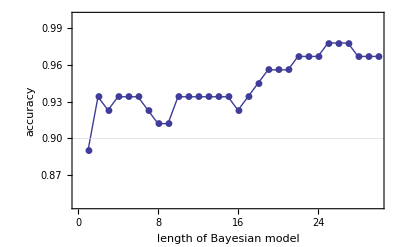

```mathematica
ListPlot[accuracies,FrameLabel->{"length of Bayesian model","accuracy"},PlotRange->{0.95*Min@accuracies,1},Joined->True,PlotMarkers->Automatic,GridLines->{{},{0.9}}]
```